## Método de Newton-Rhapson

Definición de gráfica Cobweb

```mathematica
ClearAll[CobwebPlot]
Options[CobwebPlot]=Join[{CobStyle->Automatic},Options[Graphics]];
CobwebPlot[f_,start_?NumericQ,n_,xrange:{xmin_,xmax_},opts:OptionsPattern[]]:=Module[{cob,x,g1,coor,cobstyle},
cob=NestList[f,N[start],n];
coor=Partition[Riffle[cob,cob],2,1];
coor[[1,2]]=0;
cobstyle=OptionValue[CobwebPlot,CobStyle];
cobstyle=If[cobstyle===Automatic,Red,cobstyle];
g1=Graphics[{cobstyle,Line[coor]}];
Show[{Plot[{x,f[x]},{x,xmin,xmax},PlotStyle->{{Thick,Black},Blue}],g1},FilterRules[{opts},Options[Graphics]]]]
```

Newton-Rhapson para f(x) = x^2

```mathematica
f[x_]:=x^2;
Manipulate[
CobwebPlot[#-f[#]/f'[#]&,x0,40,{0,4},PlotRange->{{0,4},{0,4}},Frame->True,Axes->False,CobStyle->Directive[Dashed,Red],PlotRangePadding->None,PlotLabel->"Cobweb: Newton-Rhapson"],
{{x0,2},0.001,4},SaveDefinitions->True
]
```

Newton-Rhapson para f(x) = Sin(x)

```mathematica
fs[x_]:=Sin[x];
Manipulate[
CobwebPlot[#-fs[#]/fs'[#]&,x0,40,{0,15},
PlotRange->{{0,6},{-6,10}},
Frame->True,Axes->False,
CobStyle->Directive[Dashed,Red],
PlotRangePadding->None,
PlotLabel->"Cobweb: Newton-Rhapson",
GridLines->{{},{0}}
],
{{x0,2},0.001,6},SaveDefinitions->True
]
```

Convergencia para f(x) = Sin(x)

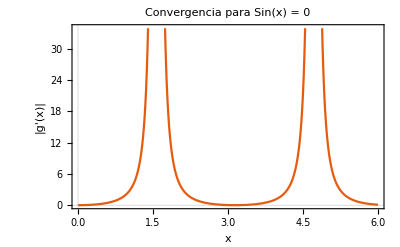

```mathematica
NewtonMap[f_,x_]:=x-f[x]/f'[x];
Convergece[f_,x_]:= Abs[D[NewtonMap[f,xx],xx] /. xx->x];
Plot[Convergece[Sin,x],{x,0,6},PlotTheme->"Scientific",PlotLabel->"Convergencia para Sin(x) = 0",FrameLabel->{"x","|g'(x)|"}]
```

Convergencia para f(x) = x^2

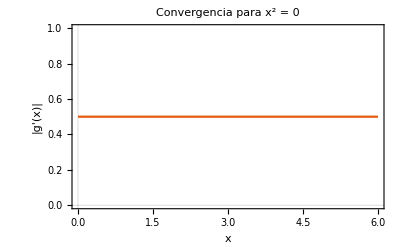

```mathematica
mf[x_]:=x^2;
Plot[Convergece[mf,x],{x,0,6},PlotTheme->"Scientific",PlotLabel->"Convergencia para x^2 = 0",FrameLabel->{"x","|g'(x)|"}]
```

Órbitas

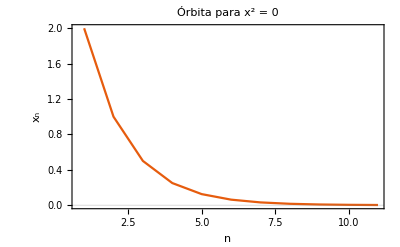

```mathematica
NewtonsMethodList[f_,{x_,x0_},n_]:=NestList[#-Function[x,f][#]/Derivative[1][Function[x,f]][#]&,x0,n];
ListLinePlot[NewtonsMethodList[x^2,{x,2},10],PlotRange->Full,PlotTheme->"Scientific",FrameLabel->{"n","x_n"},PlotLabel->"Órbita para x^2 = 0"]
```

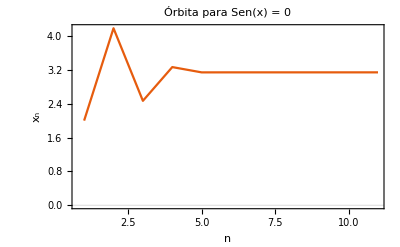

```mathematica
ListLinePlot[NewtonsMethodList[Sin[x],{x,2},10],PlotRange->Full,PlotTheme->"Scientific",FrameLabel->{"n","x_n"},PlotLabel->"Órbita para Sen(x) = 0"]
```